## Lecture 12: A systematic review of geometric transformations. Preparation for the Lab Exam

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D, DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot,RevolutionPlot3D}, ImageSize->Small,AxesLabel->{"x","y","z"}];
```

```mathematica
(* The transformations are performed by the transformation matrices and geometric transform functions. 
They apply in different ways to the vector- objects and to primitives. 
Introduce the following cases:
Vector(graphic) objects -2D,3D rotations, translations, scaling, etc. (we consider only rotations and translations)
 Primitives -2D, rotations, translations, scaling, etc.
  Translations are performed by TranslationTransform[{x,y}] or TranslationTransform[{x,y,z}]
  RotationTransform applies in 6 different versions 
  2 variants for 2D case 
  4 variants for 3D case, see the attached ppt  
The basic functions for the vector graphics are
RotationTransform
TranslationTransform
Composition- combine the transformations 
TransformationMatrix- converts the transformation into the matrix-formula. The matrices apply to vectors in the H-coordinates
[[1;;2]], [[1;;3]]  convert the H coordinates back into the Cartesian coordinates
   Evaluate- converts the matrix formula into the matrix-function  
   The primitives also use   
   RotationTransform
   TranslationTransform
   and Composition
   Further, GeometricTransformation - generates a function applied to a particular Graphics or Graphics3D object 
   The GeometricTransformation and TransformationMatrix/Evaluate are two different steps perform transforms  
for primitives and vector objects respectively.  
   The majority of the still (not moving)  plots of the vector objects are convertible to primitives by 
   Primitive=SomePlot[SomeVectorObject][[1]]. To display it use Graphics/Graphics3D[Primitive,Options]
    However, the plot is not convertible if it is a graphic function depending on a parameter such as P[a_]:=Plot[....].
   The colors and some other Options can no longer be changed. The choice depends heavily on the application.
   In this lecture we consider both options. Matrix Algebra seems to be a bit more complex, but applies 
	this way practically in any graphic system, whereas  GeometricTransformation is unique for Mathematica.             
*)
```

## Example 1 Rotate vector {x,y}={1,2} in 2D around the origin. {x,y} is a 2D vector. The vector represented by {x,y,1} and a 3x3 transformation matrix are generated

```mathematica
(* The 3x3 rotation matrix is obtained in 3 steps *)
```

```mathematica
(* Step 1: The transformation function *)
```

```mathematica
RT1=RotationTransform[a];
```

```mathematica
(* Step 2: The rotation matrix (no M1[a_] ! It is still a symbolic formula, keep "a" as the variable  *)
```

```mathematica
M1=TransformationMatrix[RT1];
```

```mathematica
MatrixForm[M1]
```

(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)

```mathematica
(* Step 3: convert the formula into the matrix-function - actionable *)
```

```mathematica
M1F[a_]:=Evaluate[M1]
```

```mathematica
(* The point {x,y} in the H-coordinates is {x,y,1} *)
```

```mathematica
Point1={1,2}; PointH1={1,2,1};
```

```mathematica
(* The rotation angle *)
```

```mathematica
an=3Pi/2;
```

```mathematica
(* Transformation in the H- coordinates *)
```

matrix . object

```mathematica
PR0[t_]:=M1F[t].PointH1
```

```mathematica
MatrixForm[PR0[t]]
```

(Cos[t]-2 Sin[t]
2 Cos[t]+Sin[t]
1)

```mathematica
(* Delete the 3d element  *)
```

```mathematica
PR[t_]:=PR0[t][[1;;2]]
```

can be used to make point based on an angle

```mathematica
(* Rotated point  *)
```

```mathematica
Point1Rot=PR[an]
```

{2,-1}

```mathematica
(* Plot the points using Graphics[Point[{..}]  *)
```

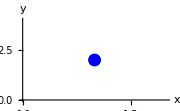

```mathematica
P1=ListPlot[{Point1}, PlotStyle->{PointSize[0.05],Blue},Axes->True]
```

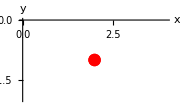

```mathematica
PRot=ListPlot[{Point1Rot}, PlotStyle->{PointSize[0.05],Red},Axes->True]
```

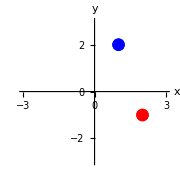

```mathematica
P12=Show[{P1,PRot},PlotRange->{{-3,3},{-3,3}},AspectRatio->1]
```

```mathematica
(* Calculate the trajectory )*)
```

```mathematica
TrajP1=Table[PR[an1],{an1,0,an,0.25}]
```

{{1.,2.},{0.474105,2.18523},{-0.0812685,2.23459},{-0.631589,2.14502},{-1.14264,1.92208},{-1.58265,1.57963},{-1.92425,1.13897},{-2.14622,0.627494},{-2.23474,0.0770038},{-2.18432,-0.478274},{-1.99809,-1.00382},{-1.68762,-1.46694},{-1.27223,-1.83886},{-0.777739,-2.09645},{-0.23489,-2.2237},{0.322563,-2.21268},{0.859961,-2.06409},{1.34389,-1.78716},{1.74426,-1.39912}}

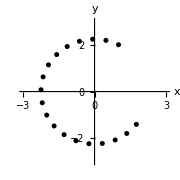

```mathematica
GTraj1=ListPlot[TrajP1,PlotStyle->{PointSize[0.02],Black},PlotRange->{{-3,3},{-3,3}},AspectRatio->1]
```

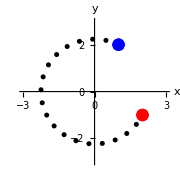

```mathematica
PointsAll=Show[GTraj1,P1,PRot]
```

```mathematica
(* Animation prep *)
```

```mathematica
L1[a_]:=ListPlot[{PR[a]},PlotRange->{{-3,3},{-3,3}},AspectRatio->1,Axes->True,ImageSize->Small,PlotStyle->{PointSize[0.05],Red}]
```

```mathematica
ShowAllL1[a_]:=Show[L1[a],PointsAll]
```

```mathematica
Manipulate[ShowAllL1[a],{a,0,an}]
```

## Example 2 : Rotate vector {x,y}={1,2} in 2D around the origin using primitives

```mathematica
Clear[P1]
```

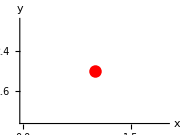

```mathematica
Graphics[{Red,PointSize[0.05],Point[{1,2}]},Axes->True,PlotRange->3,ImageSize->Small]
```

```mathematica
(* Step 1  Define the rotation transform *)
```

```mathematica
Rot[a_]:=RotationTransform[a]
```

```mathematica
Rot[a]
```

TransformationFunction[(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)]

```mathematica
(* Step 2 Instead of Transformation matrix define the transformation function *)
```

```mathematica
FRot[a_,Object_]:=GeometricTransformation[Object,Rot[a]]
```

```mathematica
(* Now apply FRot[a] with the specific angle to {1,1}. Use function P1[Color_] to indicate the color *)
```

```mathematica
P1[Color_]:={Color, PointSize[0.05],Point[{1,2}]}
```

```mathematica
FRot[0,P1[Red]]
```

GeometricTransformation[{RGBColor[1, 0, 0],PointSize[0.05],Point[{1,2}]},{{{1,0},{0,1}},{0,0}}]

```mathematica
GTraj[Color_]:={Color,PointSize[0.015],Point[TrajP1]}
```

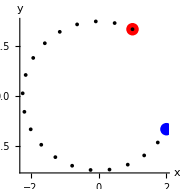

```mathematica
Graphics[{FRot[0,P1[Red]],FRot[3Pi/2,P1[Blue]],GTraj[Black]},Axes->True,PlotRange->3,ImageSize->Small]
```

```mathematica
(* Animation *)
```

```mathematica
Move2[t_]:=Graphics[{FRot[t,P1[Black]],FRot[0,P1[Red]],FRot[an,P1[Blue]],GTraj[Black]},Axes->True,PlotRange->3,ImageSize->Small]
```

```mathematica
Manipulate[Move2[t],{t,0,3Pi/2}]
```

## Example 3 : Rotate a Circle R=1 centered at {-2,-2} around point {1,2}. Use a combination of the Matrix Algebra and the primitives

translation to keep the distance between point and center
rotation to rotate the point around another point

```mathematica
(* Circle- vector *)
```

```mathematica
Paround={1,2};
```

```mathematica
R=2.5;
```

```mathematica
PC={-2,-2}
```

{-2,-2}

```mathematica
PCH={-2,-2,0}
```

{-2,-2,0}

```mathematica
Cir[t_]:=R{Cos[t],Sin[t]}
```

```mathematica
CirH[t_]:={R Cos[t],R Sin[t],1}
```

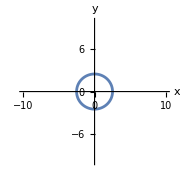

```mathematica
ParametricPlot[Cir[t],{t,0,2Pi},PlotRange->10]
```

```mathematica
(* Step 1: The Translation and rotation function *)
```

```mathematica
Clear[RT3]
```

```mathematica
RT3:=Composition[RotationTransform[a1,Paround],TranslationTransform[PC]];
```

```mathematica
(* Step 2: The rotation matrix (no M1[a1_] ! It is still a symbolic formula, keep a1 as an undefined variable  *)
```

```mathematica
MT3=TransformationMatrix[RT3]
```

{{Cos[a1],-Sin[a1],1-3 Cos[a1]+4 Sin[a1]},{Sin[a1],Cos[a1],2-4 Cos[a1]-3 Sin[a1]},{0,0,1}}

```mathematica
(* Step 3: convert the formula into the matrix-function *)
```

```mathematica
M3[a1_]:=Evaluate[MT3]
```

```mathematica
MatrixForm[M3[0]]
```

(1 | 0 | -2
0 | 1 | -2
0 | 0 | 1)

```mathematica
(* Step 4: Transform, use CirH[t_]:={Cos[t],Sin[t],1} and [[1;;2]] *)
```

```mathematica
TransCir[a_,t_]:=(M3[a].CirH[t])[[1;;2]]
```

```mathematica
TransCir[0,t]
```

{-2.+2.5 Cos[t],-2.+2.5 Sin[t]}

```mathematica
ZeroH={0,0,1};
```

```mathematica
(* Check *)
```

```mathematica
PP3=Graphics[{{Red,PointSize[0.05],Point[PC]},{Blue,PointSize[0.05],Point[Paround]}}];
```

```mathematica
MoveC3[a_]:=ParametricPlot[TransCir[a,t],{t,0,2Pi},PlotRange->7.5]
```

```mathematica
MovePC[a_]:=(M3[a].ZeroH)[[1;;2]]
```

```mathematica
L[a_]:=Graphics[Line[{{MovePC[a],Paround}}],Axes->True]
```

```mathematica
Show3[a_]:=Show[MoveC3[a],PP3]
```

```mathematica
(* Include L[a], see what happens *)
```

```mathematica
Manipulate[Show3[a],{a,0,2Pi}]
```

## Example 4 Rotate the saddle surface x^2-y^2 {x,-1,1},{y,-1,1} attached to PC4={-0.5,-0.5,-0.3} around the z direction anchored at the origin . Use the vector representation (Matrix Algebra)

```mathematica
f4[x_,y_]:=x^2-y^2
```

```mathematica
(* Convert into the parametric surface and into the H-coordinates. Note [[1;;3]] to convert it back to 3D *)
```

```mathematica
S4[u_,v_]:={u,v,f4[u,v]}
```

```mathematica
S4H[u_,v_]:={u,v,f4[u,v],1}
```

```mathematica
ParametricPlot3D[S4[u,v],{u,-1,1},{v,-1,1}]
```

-Graphics3D-

```mathematica
(* Step 1: The transformation function *)
```

matrix has to be 4 by 4 to multiply with 4 by 1

```mathematica
PC4={-0.5,-0.5,-0.3};
```

```mathematica
PC4H={-0.5,-0.5,-0.3,1}; (*4 by 1*)
```

```mathematica
Zdir4={0,0,1};Zero4={0,0,0};
```

4 by 4 matrix

rotate around the z axis and keep this distance

```mathematica
RT4=Composition[RotationTransform[a2,Zdir4] (*rotate around the z axis*)(*A1*),TranslationTransform[PC4] (*A2 distance*)]
```

TransformationFunction[(1. Cos[a2] | -1. Sin[a2] | 0 | -0.5 Cos[a2]+0.5 Sin[a2]
1. Sin[a2] | 1. Cos[a2] | 0 | -0.5 Cos[a2]-0.5 Sin[a2]
0 | 0 | 1. | -0.3
0 | 0 | 0 | 1.)]

```mathematica
MRotPoint4=RotationTransform[a3,Zdir4]
```

TransformationFunction[(Cos[a3] | -Sin[a3] | 0 | 0
Sin[a3] | Cos[a3] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]

```mathematica
(* Step 2: The rotation matrix (no M1[a_] ! It is still a symbolic formula, keep a as the variable  *)
```

```mathematica
M4=TransformationMatrix[RT4]
```

{{1. Cos[a2],-1. Sin[a2],0,-0.5 Cos[a2]+0.5 Sin[a2]},{1. Sin[a2],1. Cos[a2],0,-0.5 Cos[a2]-0.5 Sin[a2]},{0,0,1.,-0.3},{0,0,0,1.}}

```mathematica
MRot4=TransformationMatrix[MRotPoint4]
```

{{Cos[a3],-Sin[a3],0,0},{Sin[a3],Cos[a3],0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(* Step 3: convert the formula into the matrix-function *)
```

```mathematica
M4F[a2_]:=Evaluate[M4]
```

```mathematica
M4PF[a3_]:=Evaluate[MRot4]
```

```mathematica
(* Check. The new function must accept any parameter not only a1 *)
```

```mathematica
MatrixForm[M4F[ttt]] (* translate and rotate all *)
```

(1. Cos[ttt] | -1. Sin[ttt] | 0 | -0.5 Cos[ttt]+0.5 Sin[ttt]
1. Sin[ttt] | 1. Cos[ttt] | 0 | -0.5 Cos[ttt]-0.5 Sin[ttt]
0 | 0 | 1. | -0.3
0 | 0 | 0 | 1.)

```mathematica
MatrixForm[M4PF[zzz]] (*rotate *)
```

(Cos[zzz] | -Sin[zzz] | 0 | 0
Sin[zzz] | Cos[zzz] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Transformation *)
```

surface transform saddle

```mathematica
TransSad[a_,u_,v_]:=(M4F[a].S4H[u,v])[[1;;3]]
```

```mathematica
TransSad[0,0,0]
```

{-0.5,-0.5,-0.3}

```mathematica
(* Plot *)
```

```mathematica
GS4[a_]:=ParametricPlot3D[TransSad[a,u,v],{u,-1,1},{v,-1,1},PlotRange->2,Axes->True,AxesOrigin->{0,0,0},Mesh->True,MeshStyle->White]
```

```mathematica
GS4[0]
```

-Graphics3D-

```mathematica
(* Transformation *)
```

```mathematica
TransPoints4[a_]:=(M4PF[a].PC4H)[[1;;3]]
```

```mathematica
GPoints4[a_]:=Graphics3D[{{Red,PointSize[0.05],Point[TransPoints4[a]]},{Black,PointSize[0.05],Point[Zero4]}}]
```

```mathematica
(* Check *)
```

```mathematica
GPoints4[0]
```

-Graphics3D-

```mathematica
(* The direction vector : important plot Zdir4 *)
```

```mathematica
VDir=Graphics3D[{Purple,Thickness[0.01],Arrowheads[0.05],Arrow[{Zero4,Zdir4}]}]
```

-Graphics3D-

```mathematica
ShowAll4[a_]:=Show[GS4[a],GPoints4[a],VDir]
```

```mathematica
(* Check *)
```

```mathematica
ShowAll4[0]
```

-Graphics3D-

```mathematica
Manipulate[ShowAll4[a],{a,0,2Pi}]
```

## Example 5 Graphics to primitives

```mathematica
(* Almost every fixed vector graphics can be converted into the primitives 
by the function First or [[1]] i.e. Primitive=VectorGraphics[[1]]. 
Therefore, example 4 can be solved as follows.  
*)
```

```mathematica
S4[u_,v_]:={u,v,f4[u,v],1}
```

```mathematica
(* Remove all axes and the box *)
```

```mathematica
G5=ParametricPlot3D[S4[u,v][[1;;3]],{u,-1,1},{v,-1,1},Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
(* Now G5 can be displayed by Graphics3D*)
```

```mathematica
(* Step 0  Convert *)
```

```mathematica
G5P=G5[[1]];
```

```mathematica
SP5=Graphics3D[G5P]
```

-Graphics3D-

```mathematica
(* Therefore, the functions developed for primitives are applicable. Let us rotate the graph attached to 
PC5={-0.5,-0.5,-0.3} around the z-direction anchored at the origin. Use the transformation functions *)
```

```mathematica
(* Step 1  Define the transformation: rotate-translate *)
```

```mathematica
PC5={-0.5,-0.5,-0.3};
```

```mathematica
(* Composition - combine *)
```

```mathematica
RT5[a1_]:=Composition[RotationTransform[a1,Zdir4],TranslationTransform[PC5]];
```

```mathematica
RT5[a]
```

TransformationFunction[(1. Cos[a] | -1. Sin[a] | 0 | -0.5 Cos[a]+0.5 Sin[a]
1. Sin[a] | 1. Cos[a] | 0 | -0.5 Cos[a]-0.5 Sin[a]
0 | 0 | 1. | -0.3
0 | 0 | 0 | 1.)]

```mathematica
(* Step 2 Apply RT5[a] -transformation to G5P- object (surface-primitive) *)
```

```mathematica
F5[a_]:=GeometricTransformation[G5P,RT5[a]];
```

```mathematica
(* Step 3  Display the object  *)
```

```mathematica
Sur5[a_]:=Graphics3D[F5[a],Axes->True,PlotRange->2]
```

```mathematica
(* Check  *)
```

```mathematica
Sur5[Pi]
```

-Graphics3D-

```mathematica
(* Add the points from example 4 including the rotating point PC5 *)
```

```mathematica
(* Step 1  Define the transformation for PC5 - only the rotation *)
```

```mathematica
PC5={-0.5,-0.5,-0.3};
```

```mathematica
(* Rotate around z (anything) *)
```

```mathematica
RPoint5[a_]:=RotationTransform[a,Zdir4];
```

```mathematica
RPoint5[a]
```

TransformationFunction[(Cos[a] | -Sin[a] | 0 | 0
Sin[a] | Cos[a] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]

```mathematica
(* Step 2 Define the objects and apply RPoint5[a] to primitive Point[PC5]  *)
```

```mathematica
OP5:={Red,PointSize[0.05],Point[PC5]}
```

```mathematica
FPoint5[a_]:=GeometricTransformation[OP5,RPoint5[a]];
```

```mathematica
Zero5={Black,PointSize[0.05],Point[Zero4]}
```

{GrayLevel[0],PointSize[0.05],Point[{0,0,0}]}

```mathematica
VDir5={Purple,Thickness[0.01],Arrowheads[0.05],Arrow[{Zero4,Zdir4}]}
```

{RGBColor[0.5, 0, 0.5],Thickness[0.01],Arrowheads[0.05],Arrow[{{0,0,0},{0,0,1}}]}

```mathematica
ShowAll5[a_]:=Graphics3D[{F5[a] (*sf*),FPoint5[a] (*red*),Zero5,VDir5},Axes->True,AxesOrigin->{0,0,0},PlotRange->2]
```

```mathematica
ShowAll5[Pi]
```

-Graphics3D-

```mathematica
Manipulate[ShowAll5[a],{a,0,2Pi}]
```

## (* Intro into STL *)

face wtih many connection -> count in counter clockwise

```mathematica
(* One of the most important industrial formats is StereoLithorgraphy *) 
(* The name STL is an acronym that stands for stereolithography. This is the most a popular format for the 3D printing technology. It is also referred to as Standard Triangle Language or Standard Tessellation Language. *) 
(* An example of the STL file is below. Each triple is a facet triangle and the "outerloop" means that the vertices are listed in counterclockwise order when looking at the object from the outside (right-hand rule). The facet normal can be omitted: 0 0 0  *) 
(* There are many options(Import elements) to read different structures of the STL file
The MeshRegion is the default option *)
```

```mathematica
(* -Graphics-*)
```

```mathematica
SetDirectory["D:\\SIIT\\CG\\2024\\L12"]
```

D:\SIIT\CG\2024\L12

```mathematica
(* Import the STL files  solid.stl  and spikeymodel.stl *)
```

```mathematica
Ex1=Import["solid.stl","PolygonObjects"];
```

```mathematica
(* Display *)
```

```mathematica
Graphics3D[Ex1]
```

-Graphics3D-

```mathematica
(* Print the structure *)
```

```mathematica
FilePrint["solid.stl"]
```

solid Created_by_the_Wolfram_Language_:_www.wolfram.com
 facet normal 0 0 0
  outer loop
  vertex 1 -1 0
  vertex -1 -1 0
  vertex 1 1 0
  endloop
 endfacet

 facet normal 0 0 0
  outer loop
  vertex -1 -1 0
  vertex 1 -1 0
  vertex 0 0 1
  endloop
 endfacet

 facet normal 0 0 0
  outer loop
  vertex 1 -1 0
  vertex 1 1 0
  vertex 0 0 1
  endloop
 endfacet

 facet normal 0 0 0
  outer loop
  vertex 0 0 1
  vertex 1 1 0
  vertex -1 1 0
  endloop
 endfacet

 facet normal 0 0 0
  outer loop
  vertex 1 1 0
  vertex -1 -1 0
  vertex -1 1 0
  endloop
 endfacet

 facet normal 0 0 0
  outer loop
  vertex -1 -1 0
  vertex 0 0 1
  vertex -1 1 0
  endloop
 endfacet

endsolid Created_by_the_Wolfram_Language_:_www.wolfram.com

```mathematica
Spikey=Import["spikeymodel.stl","PolygonObjects"];
```

```mathematica
Graphics3D[Spikey]
```

-Graphics3D-

```mathematica
(* Combine Graphics3D *)
```

```mathematica
Sphere1={Yellow,Opacity[0.2],Sphere[{0,0,0},2]};
```

```mathematica
Zero={Red,PointSize[0.08],Point[{0,0,0}]};
```

```mathematica
Comb1=Graphics3D[{{Opacity[0.5],Spikey},Sphere1,Zero},Axes->True]
```

-Graphics3D-

```mathematica
(* The geometric transformations are applicable.  The STL objects are compatible with Graphics3D. 
They are compatible with graphic objects too today we do not have time for that   *)
```

## Example 6 Rotate Comb1 around x with the anchor point {0,0,0} at the distance 3.5 from the center of rotation

```mathematica
(* Step 1 Clean  *)
```

```mathematica
Comb2={{Opacity[0.5],Spikey},Sphere1,Zero}; (* no Graphics3D !*)
```

```mathematica
(* Step 2 Rotate around x and Translate by 2.5 along z *)
```

```mathematica
Rot6[a_]:=GeometricTransformation[Comb2,Composition[RotationTransform[a,{1,0,0}],TranslationTransform[{0,0,2.5}]]];
```

```mathematica
G6[a_]:=Graphics3D[{Zero,Rot6[a]},Axes->True,PlotRange->4.5,AxesOrigin->{0,0,0},Boxed->False]
```

```mathematica
(* Check  *)
```

```mathematica
G6[Pi]
```

-Graphics3D-

```mathematica
(* Animate  *)
```

```mathematica
Manipulate[G6[a],{a,0,2Pi}]
```